# Fitting Motor Velocity Data

Cole Welch
26 August 2018

We explore extracting time constants from motor model expressions.

## Section. Introduction

### Section.Subsection. Administrivia

Before we begin, we load in some previously computed logic (Ref: https://github.com/rgatkinson/RobotPhysics/blob/master/MotorPhysics-GearsInitialConditions.pdf)

```mathematica
Get[NotebookDirectory[] <> "Utilities.m"]
inputDirectory = FileNameJoin[{NotebookDirectory[],"MotorPhysicsGearsInitialConditions.Output"}] <> $PathnameSeparator;
Get[inputDirectory <> "ParametersUnitsAndAssumptions.m"];
Get[inputDirectory <> "MotorModels.m"];
Get[inputDirectory <> "MotorTimeDomainFunctions.m"];
Get[inputDirectory <> "Misc.m"];
```

```mathematica
SetOptions[Plot,LabelStyle->Directive[Background->None]];
prettyPrintFontSize = 20;
framed[expr_] := Framed[expr, FrameStyle->Darker[Green]]
```

## 2. Motor Velocity Expression

Let’s refresh ourselves as to the parameter values of sample AndyMark 40s.

```mathematica
motorParameters["AM 40 A"]//N
```

<|R→2.5 W/A^2,L→0.000674 H,Ν→40.,η→0.9,Ke→0.018825 kg m^2/(s^2 A rad),Kt→0.018825 kg m^2/(s^2 A rad),B→0.000157569 kg m^2/(s rad^2),J→1.54236×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

```mathematica
motorParameters["AM 40 B"]//N
```

<|R→3.8 W/A^2,L→0.000705 H,Ν→40.,η→0.9,Ke→0.017625 kg m^2/(s^2 A rad),Kt→0.017625 kg m^2/(s^2 A rad),B→0.000388889 kg m^2/(s rad^2),J→1.20903×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

```mathematica
motorParameters["AM 40 C"]//N
```

<|R→2.1 W/A^2,L→0.000716 H,Ν→40.,η→0.9,Ke→0.019075 kg m^2/(s^2 A rad),Kt→0.019075 kg m^2/(s^2 A rad),B→0.0000125 kg m^2/(s rad^2),J→1.71597×10^-8 kg m^2/rad^2,Jafter→0. kg m^2/rad^2,Bafter→0. kg m^2/(s rad^2),ΔτappConst→0. kg m^2/(s^2 rad)|>

We show a list of the variables present in our expression for the velocity time domain expression for a motor.

```mathematica
velAfterStepGeneric // variables
```

{B,Bafter,J,Jafter,Ke,Kt,L,R,t,vapp0,ΔvappConst,ΔτappConst,η,Ν,τapp0}

We substitute what we know about our situation. However, we do not simply plug in “AM 40 A/B/C,” since some of our parameters are going to be different from those of a general motor. We also average each of the parameter values we do use over all the motors that have already been tested.

```mathematica
velSubExpr=velAfterStepGeneric/.{B->0.000186,J->1.49*10^-8,Ke->0.0184,Kt->0.0184,L->0.000697,R->1.2,vapp0->0,ΔvappConst->13,ΔτappConst->0,τapp0->0,Ν->40}//FullSimplify//N
```

-((0.0133378 (Jafter+0.00002384 η) η ((-1.+2.71828^((t (-0.5 Bafter-860.832 Jafter-0.169322 η+717.36 √(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))/(Jafter+0.00002384 η)))/(0.000697 Bafter+1.2 Jafter+0.000236035 η-1. √(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2))-(1. (-1.+2.71828^(-(717.36 t (0.000697 Bafter+1.2 Jafter+0.000236035 η+√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))/(Jafter+0.00002384 η))))/(0.000697 Bafter+1.2 Jafter+0.000236035 η+√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2))))/(√(4.85809×10^-7 Bafter^2-0.0016728 Bafter Jafter+1.44 Jafter^2+2.49274×10^-7 Bafter η-0.00193941 Jafter η-4.02802×10^-9 η^2)))

## 3. Data Fitting

#### 3.1. Data Set 1

We are now ready to import the motor velocity step response data that we are going to fit. Note: we have to remove the extra set of brackets on the table to use the data.

```mathematica
data1=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",1}]
```

{{0.,0.},{0.008,0.},{0.016,62.5},{0.024,402.778},{0.032,617.188},{0.04,720.},{0.048,830.},{0.056,925.},{0.064,1025.},{0.072,1120.},{0.08,1235.},{0.088,1365.},{0.096,1495.},{0.104,1590.},{0.112,1670.},{0.12,1730.},{0.128,1770.},{0.136,1790.},{0.144,1830.},{0.152,1865.},{0.16,1935.},{0.168,1990.},{0.176,2050.},{0.184,2090.},{0.192,2130.},{0.2,2100.},{0.208,2100.},{0.216,2100.},{0.224,2100.},{0.232,2100.},{0.24,2130.},{0.248,2155.},{0.256,2185.},{0.264,2225.},{0.272,2270.},{0.28,2325.},{0.288,2370.},{0.296,2410.},{0.304,2450.},{0.312,2490.},{0.32,2515.},{0.328,2535.},{0.336,2565.},{0.344,2585.},{0.352,2590.},{0.36,2615.},{0.368,2640.},{0.376,2645.},{0.384,2655.},{0.392,2670.},{0.4,2680.},{0.408,2695.},{0.416,2715.},{0.424,2730.},{0.432,2745.},{0.44,2745.},{0.448,2745.},{0.456,2750.},{0.464,2750.},{0.472,2760.},{0.48,2775.},{0.488,2785.},{0.496,2785.},{0.504,2805.},{0.512,2815.},{0.52,2825.},{0.528,2835.},{0.536,2855.},{0.544,2855.},{0.552,2850.},{0.56,2845.},{0.568,2835.},{0.576,2825.},{0.584,2815.},{0.592,2815.},{0.6,2820.},{0.608,2830.},{0.616,2835.},{0.624,2850.},{0.632,2860.},{0.64,2865.},{0.648,2875.},{0.656,2880.},{0.664,2880.},{0.672,2885.},{0.68,2890.},{0.688,2885.},{0.696,2890.},{0.704,2895.},{0.712,2895.},{0.72,2900.},{0.728,2905.},{0.736,2900.},{0.744,2900.},{0.752,2885.},{0.76,2870.},{0.768,2870.},{0.776,2880.},{0.784,2880.},{0.792,2910.},{0.8,2925.},{0.808,2930.},{0.816,2930.},{0.824,2935.},{0.832,2925.},{0.84,2920.},{0.848,2920.},{0.856,2910.},{0.864,2900.},{0.872,2890.},{0.88,2895.},{0.888,2885.},{0.896,2895.},{0.904,2905.},{0.912,2910.},{0.92,2900.},{0.928,2905.},{0.936,2895.},{0.944,2885.},{0.952,2885.},{0.96,2890.},{0.968,2895.},{0.976,2920.},{0.984,2945.},{0.992,2960.},{1.,2975.},{1.008,2980.},{1.016,2955.},{1.024,2925.},{1.032,2905.},{1.04,2890.},{1.048,2880.},{1.056,2885.},{1.064,2900.},{1.072,2910.},{1.08,2915.},{1.088,2925.},{1.096,2935.},{1.104,2940.},{1.112,2940.},{1.12,2935.},{1.128,2920.},{1.136,2910.},{1.144,2900.},{1.152,2895.},{1.16,2895.},{1.168,2905.},{1.176,2910.},{1.184,2920.},{1.192,2930.},{1.2,2945.},{1.208,2950.},{1.216,2950.},{1.224,2935.},{1.232,2925.},{1.24,2910.},{1.248,2900.},{1.256,2895.},{1.264,2905.},{1.272,2910.},{1.28,2915.},{1.288,2925.},{1.296,2935.},{1.304,2940.},{1.312,2935.},{1.32,2930.},{1.328,2925.},{1.336,2915.},{1.344,2905.},{1.352,2910.},{1.36,2915.},{1.368,2905.},{1.376,2905.},{1.384,2920.},{1.392,2925.},{1.4,2935.},{1.408,2955.},{1.416,2975.},{1.424,2965.},{1.432,2965.},{1.44,2960.},{1.448,2955.},{1.456,2950.},{1.464,2955.},{1.472,2960.},{1.48,2965.},{1.488,2970.},{1.496,2955.},{1.504,2950.},{1.512,2935.},{1.52,2910.},{1.528,2885.},{1.536,2890.},{1.544,2890.},{1.552,2900.},{1.56,2915.},{1.568,2940.},{1.576,2940.},{1.584,2945.},{1.592,2940.},{1.6,2955.},{1.608,2945.},{1.616,2955.},{1.624,2950.},{1.632,2950.},{1.64,2930.},{1.648,2930.},{1.656,2915.},{1.664,2915.},{1.672,2920.},{1.68,2935.},{1.688,2945.},{1.696,2955.},{1.704,2960.},{1.712,2960.},{1.72,2945.},{1.728,2930.},{1.736,2920.},{1.744,2910.},{1.752,2895.},{1.76,2890.},{1.768,2890.},{1.776,2900.},{1.784,2905.},{1.792,2915.},{1.8,2925.},{1.808,2930.},{1.816,2920.},{1.824,2925.},{1.832,2930.},{1.84,2940.},{1.848,2950.},{1.856,2960.},{1.864,2955.},{1.872,2950.},{1.88,2935.},{1.888,2910.},{1.896,2885.},{1.904,2870.},{1.912,2855.},{1.92,2850.},{1.928,2870.},{1.936,2910.},{1.944,2940.},{1.952,2975.},{1.96,3005.},{1.968,3010.}}

Change the velocity units from ticks / second to radians / second.

```mathematica
data1={#[[1]],2Pi/1120*#[[2]]}&/@data1
```

{{0.,0.},{0.008,0.},{0.016,0.350624},{0.024,2.25958},{0.032,3.46241},{0.04,4.03919},{0.048,4.65629},{0.056,5.18924},{0.064,5.75024},{0.072,6.28319},{0.08,6.92833},{0.088,7.65763},{0.096,8.38693},{0.104,8.91988},{0.112,9.36868},{0.12,9.70528},{0.128,9.92968},{0.136,10.0419},{0.144,10.2663},{0.152,10.4626},{0.16,10.8553},{0.168,11.1639},{0.176,11.5005},{0.184,11.7249},{0.192,11.9493},{0.2,11.781},{0.208,11.781},{0.216,11.781},{0.224,11.781},{0.232,11.781},{0.24,11.9493},{0.248,12.0895},{0.256,12.2578},{0.264,12.4822},{0.272,12.7347},{0.28,13.0432},{0.288,13.2957},{0.296,13.5201},{0.304,13.7445},{0.312,13.9689},{0.32,14.1091},{0.328,14.2213},{0.336,14.3896},{0.344,14.5018},{0.352,14.5299},{0.36,14.6701},{0.368,14.8104},{0.376,14.8384},{0.384,14.8945},{0.392,14.9787},{0.4,15.0348},{0.408,15.1189},{0.416,15.2311},{0.424,15.3153},{0.432,15.3994},{0.44,15.3994},{0.448,15.3994},{0.456,15.4275},{0.464,15.4275},{0.472,15.4836},{0.48,15.5677},{0.488,15.6238},{0.496,15.6238},{0.504,15.736},{0.512,15.7921},{0.52,15.8482},{0.528,15.9043},{0.536,16.0165},{0.544,16.0165},{0.552,15.9885},{0.56,15.9604},{0.568,15.9043},{0.576,15.8482},{0.584,15.7921},{0.592,15.7921},{0.6,15.8202},{0.608,15.8763},{0.616,15.9043},{0.624,15.9885},{0.632,16.0446},{0.64,16.0726},{0.648,16.1287},{0.656,16.1568},{0.664,16.1568},{0.672,16.1848},{0.68,16.2129},{0.688,16.1848},{0.696,16.2129},{0.704,16.2409},{0.712,16.2409},{0.72,16.269},{0.728,16.297},{0.736,16.269},{0.744,16.269},{0.752,16.1848},{0.76,16.1007},{0.768,16.1007},{0.776,16.1568},{0.784,16.1568},{0.792,16.3251},{0.8,16.4092},{0.808,16.4373},{0.816,16.4373},{0.824,16.4653},{0.832,16.4092},{0.84,16.3812},{0.848,16.3812},{0.856,16.3251},{0.864,16.269},{0.872,16.2129},{0.88,16.2409},{0.888,16.1848},{0.896,16.2409},{0.904,16.297},{0.912,16.3251},{0.92,16.269},{0.928,16.297},{0.936,16.2409},{0.944,16.1848},{0.952,16.1848},{0.96,16.2129},{0.968,16.2409},{0.976,16.3812},{0.984,16.5214},{0.992,16.6056},{1.,16.6897},{1.008,16.7178},{1.016,16.5775},{1.024,16.4092},{1.032,16.297},{1.04,16.2129},{1.048,16.1568},{1.056,16.1848},{1.064,16.269},{1.072,16.3251},{1.08,16.3531},{1.088,16.4092},{1.096,16.4653},{1.104,16.4934},{1.112,16.4934},{1.12,16.4653},{1.128,16.3812},{1.136,16.3251},{1.144,16.269},{1.152,16.2409},{1.16,16.2409},{1.168,16.297},{1.176,16.3251},{1.184,16.3812},{1.192,16.4373},{1.2,16.5214},{1.208,16.5495},{1.216,16.5495},{1.224,16.4653},{1.232,16.4092},{1.24,16.3251},{1.248,16.269},{1.256,16.2409},{1.264,16.297},{1.272,16.3251},{1.28,16.3531},{1.288,16.4092},{1.296,16.4653},{1.304,16.4934},{1.312,16.4653},{1.32,16.4373},{1.328,16.4092},{1.336,16.3531},{1.344,16.297},{1.352,16.3251},{1.36,16.3531},{1.368,16.297},{1.376,16.297},{1.384,16.3812},{1.392,16.4092},{1.4,16.4653},{1.408,16.5775},{1.416,16.6897},{1.424,16.6336},{1.432,16.6336},{1.44,16.6056},{1.448,16.5775},{1.456,16.5495},{1.464,16.5775},{1.472,16.6056},{1.48,16.6336},{1.488,16.6617},{1.496,16.5775},{1.504,16.5495},{1.512,16.4653},{1.52,16.3251},{1.528,16.1848},{1.536,16.2129},{1.544,16.2129},{1.552,16.269},{1.56,16.3531},{1.568,16.4934},{1.576,16.4934},{1.584,16.5214},{1.592,16.4934},{1.6,16.5775},{1.608,16.5214},{1.616,16.5775},{1.624,16.5495},{1.632,16.5495},{1.64,16.4373},{1.648,16.4373},{1.656,16.3531},{1.664,16.3531},{1.672,16.3812},{1.68,16.4653},{1.688,16.5214},{1.696,16.5775},{1.704,16.6056},{1.712,16.6056},{1.72,16.5214},{1.728,16.4373},{1.736,16.3812},{1.744,16.3251},{1.752,16.2409},{1.76,16.2129},{1.768,16.2129},{1.776,16.269},{1.784,16.297},{1.792,16.3531},{1.8,16.4092},{1.808,16.4373},{1.816,16.3812},{1.824,16.4092},{1.832,16.4373},{1.84,16.4934},{1.848,16.5495},{1.856,16.6056},{1.864,16.5775},{1.872,16.5495},{1.88,16.4653},{1.888,16.3251},{1.896,16.1848},{1.904,16.1007},{1.912,16.0165},{1.92,15.9885},{1.928,16.1007},{1.936,16.3251},{1.944,16.4934},{1.952,16.6897},{1.96,16.858},{1.968,16.8861}}

Here is a plot of the data.

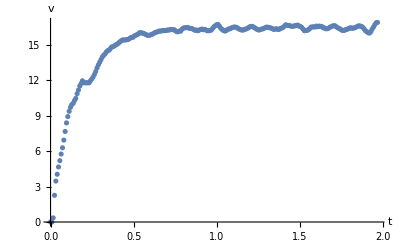

```mathematica
ListPlot[data1,AxesLabel->{t,v}]
```

```mathematica
Length[data1]
```

247

We’re ready to fit.

```mathematica
nlm1=NonlinearModelFit[data1,velSubExpr,{Bafter,Jafter,η},t]
```

FittedModel[-0.455857 (-0.135209 (-1.+2.71828^(-1715.7 t))+36.0785 (-1.+2.71828^(-6.4298 t)))]

Here is a comparison between the data and our fit.  They appear to follow each other quite closely.

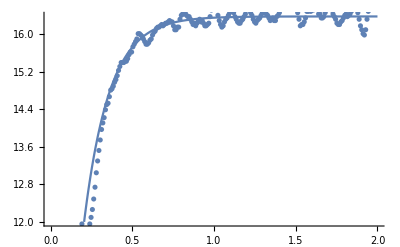

```mathematica
Show[Plot[nlm1[t],{t,0,2}],ListPlot[data1], AxesOrigin->{0,0},PlotRangePadding->{0.1,12}]
```

Here are our fit parameters.  However, they are clearly incorrect.

```mathematica
nlm1["BestFitParameters"]
```

{Bafter→-10.684,Jafter→3.0914,η→40.7181}

#### 3.1. Data Set 2

We repeat the steps from Data Set 1 for our remaining data sets.

```mathematica
data2=Import["C:\RobotPhysics\3 Wheel Robot Encoder Rotational Velocity Test Data.xlsx",{"Data",2}]
```

{{1.,2.,3.}}

```mathematica
data2={#[[1]],2Pi/1120*#[[2]]}&/@data2
```

{{1.,0.01122}}

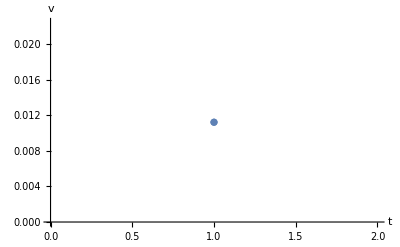

```mathematica
ListPlot[data2,AxesLabel->{t,v}]
```

```mathematica
Length[data2]
```

1

```mathematica
nlm2=NonlinearModelFit[data2,velSubExpr,{Bafter,Jafter,η},t]
```

FittedModel[-0.000034106 (-0.301133 (-1.+2.71828^(-1721.66 t))+524.371 (-1.+2.71828^(-0.988708 t)))]

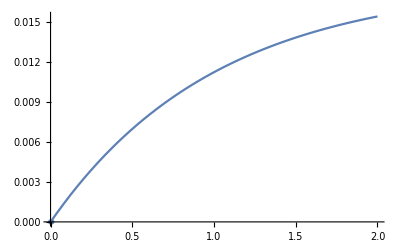

```mathematica
Show[Plot[nlm2[t],{t,0,2}],ListPlot[data1], AxesOrigin->{0,0},PlotRangePadding->{0.1,12}]
```

## Section. Revision History

2018.08.26. Initial version.

2018.08.28. Added velocity expression.  Added motor data.  Created NonlinearModelFit for the data.

2018.08.29. Fixed issue with some variables not being plugged in to velAfterStepGeneric. Changed units on data from ticks / sec to rad / sec.

2018.08.30. Fixed drastically incorrect scale on fit (issue was due to constants being specified with incorrect units or after the gearbox instead of before).